```mathematica
(* Student Name *)
(* June 28, 2017 *)
(* MITES Physics III: Intro to Oscillations and Waves *)
(* Various Plots of Damped Oscillations *)

(* Write code which documents the three different types of damped motion possible *)
```

0.5

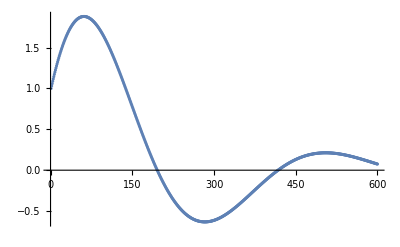

```mathematica
(*Underdamped*)

x0 = 1.0; (* Defines the initial position of the mass *) 

xdot0 = 3.0; (* Defines the initial velocity of the mass *) 

e = 0.01; (* Defines how much we increment by time *) 

ω = Sqrt[5]; γ = 0.5

xvalues= ConstantArray[0,600]; (* Defines an empty array of values for our position *) 

xdotvalues= ConstantArray[0,600]; (* Defines an empty array of values for our velocity *) 

xvalues[[1]] = x0; (* Sets first value of position array to the defined initial position *) 

xdotvalues[[1]] = xdot0; (* Sets first value of velocity array to the defined initial velocity *) 

For[i=2, (* Sets initial value of for loop *) 
i<601, (* Condition for for increment of for loop *) 
i++, (* Increment for loop by a single index *) 
xvalues[[i]] = xvalues[[i-1]]+e*xdotvalues[[i-1]]; (* Defines next x value as a first order Taylor series approximation of the position *) 
xdotvalues[[i]] = xdotvalues[[i-1]]- e*(ω xvalues[[i-1]]+2 γ xdotvalues[[i-1]] ) ] (* Defines next velocity value as a first order Taylor series approximation of the velocity *) 
ListPlot[xvalues] (* Plots the list of xvalues to yield a position as a function of time plot *)
```

5.

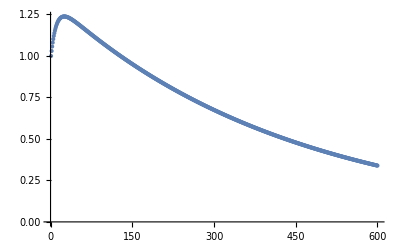

```mathematica
(*Critically Damped*)

x0 = 1.0; (* Defines the initial position of the mass *) 

xdot0 = 3.0; (* Defines the initial velocity of the mass *) 

e = 0.01; (* Defines how much we increment by time *) 

ω = Sqrt[5]; γ = 5.0

xvalues= ConstantArray[0,600]; (* Defines an empty array of values for our position *) 

xdotvalues= ConstantArray[0,600]; (* Defines an empty array of values for our velocity *) 

xvalues[[1]] = x0; (* Sets first value of position array to the defined initial position *) 

xdotvalues[[1]] = xdot0; (* Sets first value of velocity array to the defined initial velocity *) 

For[i=2, (* Sets initial value of for loop *) 
i<601, (* Condition for for increment of for loop *) 
i++, (* Increment for loop by a single index *) 
xvalues[[i]] = xvalues[[i-1]]+e*xdotvalues[[i-1]]; (* Defines next x value as a first order Taylor series approximation of the position *) 
xdotvalues[[i]] = xdotvalues[[i-1]]- e*(ω xvalues[[i-1]]+2 γ xdotvalues[[i-1]] ) ] (* Defines next velocity value as a first order Taylor series approximation of the velocity *) 
ListPlot[xvalues] (* Plots the list of xvalues to yield a position as a function of time plot *)
```

5.

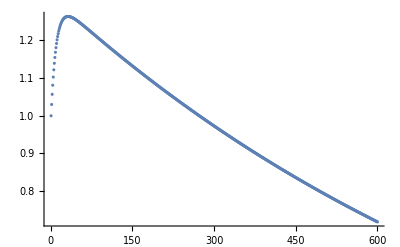

```mathematica
(*Overdamped*)

x0 = 1.0; (* Defines the initial position of the mass *) 

xdot0 = 3.0; (* Defines the initial velocity of the mass *) 

e = 0.01; (* Defines how much we increment by time *) 

ω = 1.0; γ = 5.0

xvalues= ConstantArray[0,600]; (* Defines an empty array of values for our position *) 

xdotvalues= ConstantArray[0,600]; (* Defines an empty array of values for our velocity *) 

xvalues[[1]] = x0; (* Sets first value of position array to the defined initial position *) 

xdotvalues[[1]] = xdot0; (* Sets first value of velocity array to the defined initial velocity *) 

For[i=2, (* Sets initial value of for loop *) 
i<601, (* Condition for for increment of for loop *) 
i++, (* Increment for loop by a single index *) 
xvalues[[i]] = xvalues[[i-1]]+e*xdotvalues[[i-1]]; (* Defines next x value as a first order Taylor series approximation of the position *) 
xdotvalues[[i]] = xdotvalues[[i-1]]- e*(ω xvalues[[i-1]]+2 γ xdotvalues[[i-1]] ) ] (* Defines next velocity value as a first order Taylor series approximation of the velocity *) 
ListPlot[xvalues] (* Plots the list of xvalues to yield a position as a function of time plot *)
```